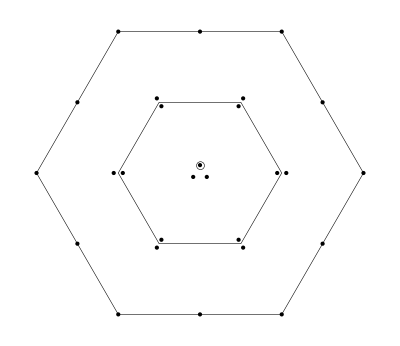

Y=0,  I_3=0

-6uuūū-2ddd̄d̄-2sss̄s̄+3(ud+du)(ūd̄+d̄ū)+3(us+su)(ūs̄+s̄ū)-(sd+ds)(s̄d̄+d̄s̄)

```mathematica
(*-------------------------------*)
```

The current J:

-((d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T))-(d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_b 1C((s̄)_a)^T)-(d_a^T C1 s_b+s_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)-(d_a^T C1 s_b+s_a^T C1 d_b) ((s̄)_b 1C((d̄)_a)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_a 1C((ū)_b)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_b 1C((ū)_a)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((ū)_a 1C((d̄)_b)^T)+3 (d_a^T C1 u_b+u_a^T C1 d_b) ((ū)_b 1C((d̄)_a)^T)-2 (d_a^T C1 d_b) ((d̄)_a 1C((d̄)_b)^T+(d̄)_b 1C((d̄)_a)^T)+3 (s_a^T C1 u_b+u_a^T C1 s_b) ((s̄)_a 1C((ū)_b)^T)+3 (s_a^T C1 u_b+u_a^T C1 s_b) ((s̄)_b 1C((ū)_a)^T)+3 (s_a^T C1 u_b+u_a^T C1 s_b) ((ū)_a 1C((s̄)_b)^T)+3 (s_a^T C1 u_b+u_a^T C1 s_b) ((ū)_b 1C((s̄)_a)^T)-2 (s_a^T C1 s_b) ((s̄)_a 1C((s̄)_b)^T+(s̄)_b 1C((s̄)_a)^T)-6 (u_a^T C1 u_b) ((ū)_a 1C((ū)_b)^T+(ū)_b 1C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 d-d̄ γ^μ d d̄ γ^μ d+d̄(γ̄)^5 d-1/2 (d̄ σ^μν d d̄ σ^μν d)-d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s-d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d-d̄ γ^μ d s̄ γ^μ s-d̄ γ^μ s s̄ γ^μ d+d̄(γ̄)^5 s s̄(γ̄)^5 d-1/2 (d̄ σ^μν d s̄ σ^μν s)-1/2 (d̄ σ^μν s s̄ σ^μν d)+(d̄(γ̄)^5 d) (s̄(γ̄)^5 s-3 (ū(γ̄)^5 u))+(d̄ 1d) (s̄ 1s-3 (ū 1u))+d̄ 1s s̄ 1d+3 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)+3 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)+3 (d̄ γ^μ d ū γ^μ u)+3 (d̄ γ^μ u ū γ^μ d)-3 (d̄(γ̄)^5 u ū(γ̄)^5 d)+3/2 (d̄ σ^μν d ū σ^μν u)+3/2 (d̄ σ^μν u ū σ^μν d)-3 (d̄ 1u ū 1d)+d̄ 1d d̄ 1d-s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s-s̄ γ^μ s s̄ γ^μ s+s̄(γ̄)^5 s-1/2 (s̄ σ^μν s s̄ σ^μν s)+3 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)+3 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)+3 (s̄ γ^μ s ū γ^μ u)+3 (s̄ γ^μ u ū γ^μ s)-3 (s̄(γ̄)^5 s ū(γ̄)^5 u)-3 (s̄(γ̄)^5 u ū(γ̄)^5 s)+3/2 (s̄ σ^μν s ū σ^μν u)+3/2 (s̄ σ^μν u ū σ^μν s)-3 (s̄ 1s ū 1u)-3 (s̄ 1u ū 1s)+s̄ 1s s̄ 1s-3 (ū(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)-3 (ū γ^μ u ū γ^μ u)+3 (ū(γ̄)^5 u ū(γ̄)^5 u)-3/2 (ū σ^μν u ū σ^μν u)+3 (ū 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(64 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(16 π^5)-(3 ⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s+4 m_u) q^4)/π^4-(⟨ d̄ d⟩ log(-q^2/μ^2) (8 m_d+m_s+9 m_u) q^4)/(3 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (m_d+8 m_s+9 m_u) q^4)/(3 π^4)-(20 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(20 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(12 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(144 π^6)-(44 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(60 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(60 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(2 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(3 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2-(21 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(3 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(2 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2-(21 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2-(21 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(21 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(6 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(10 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(3 π q^2)-(10 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(3 π q^2)-(14 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)+(97 ⟨ d̄ Gd⟩^2)/(288 π^2 q^2)+(97 ⟨ s̄ Gs⟩^2)/(288 π^2 q^2)+(121 ⟨ ū Gu⟩^2)/(32 π^2 q^2)-(6 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)+(10 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)+(10 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)+(61 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(288 π^2 q^2)+(157 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(32 π^2 q^2)+(157 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(32 π^2 q^2)-(4 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (40 m_d-4 m_s))/(9 q^2)-(4 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (40 m_s-4 m_d))/(9 q^2)-(4 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (-4 m_d-56 m_u))/q^2-(4 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (-4 m_s-56 m_u))/q^2+(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (m_d+m_s-3 m_u))/q^2+(4 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (24 m_d+4 m_u))/q^2+(4 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (24 m_s+4 m_u))/q^2

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

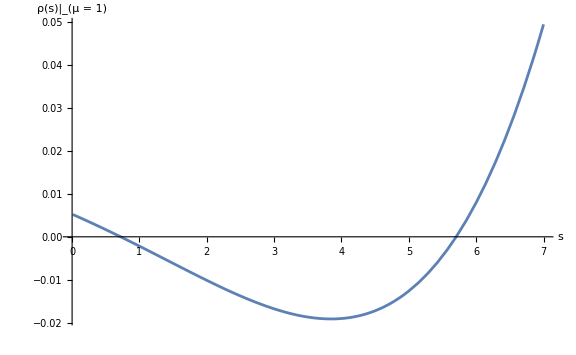
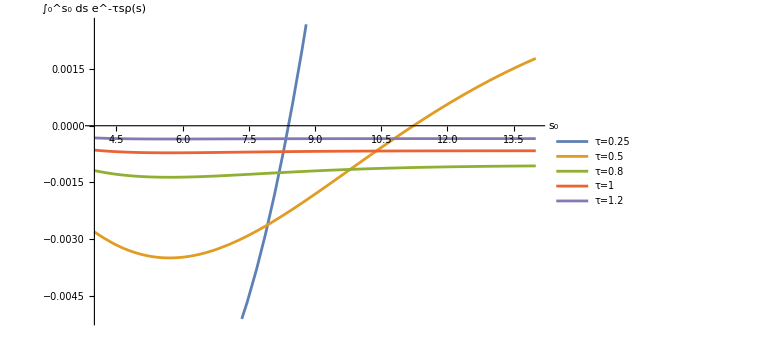

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

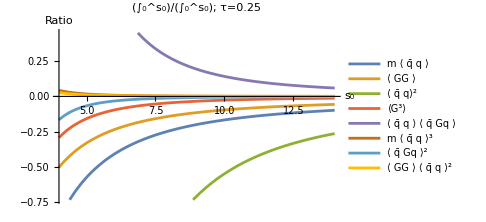
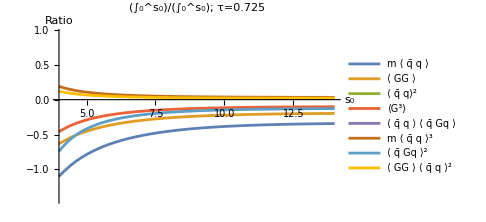
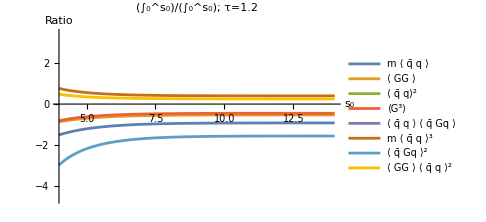

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

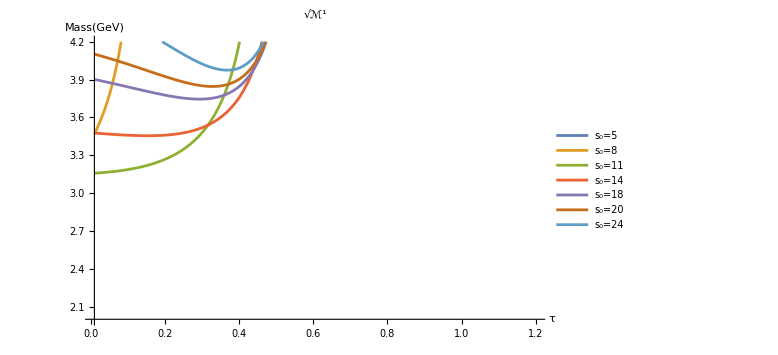
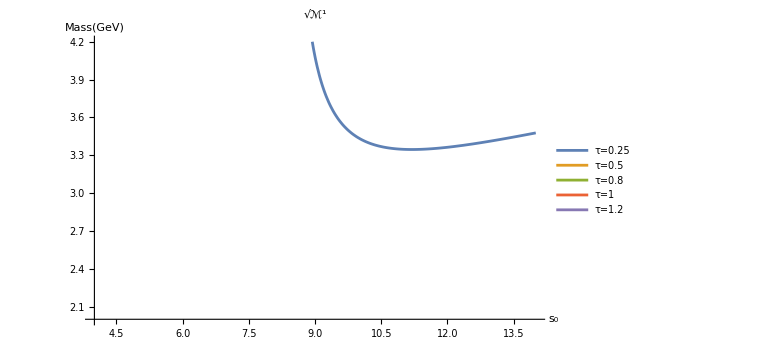

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

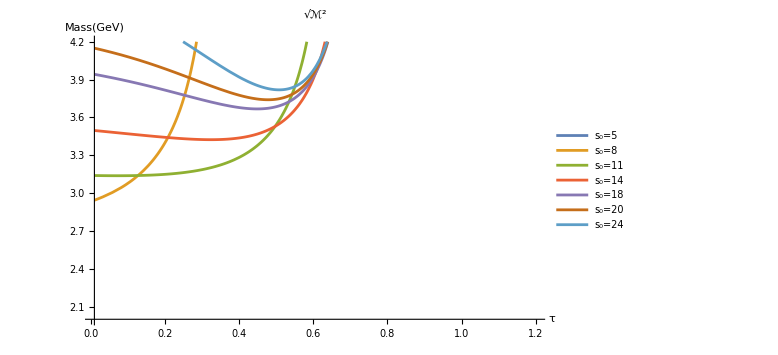
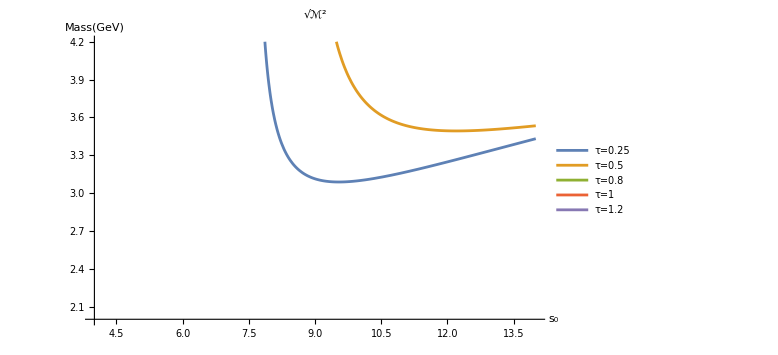

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

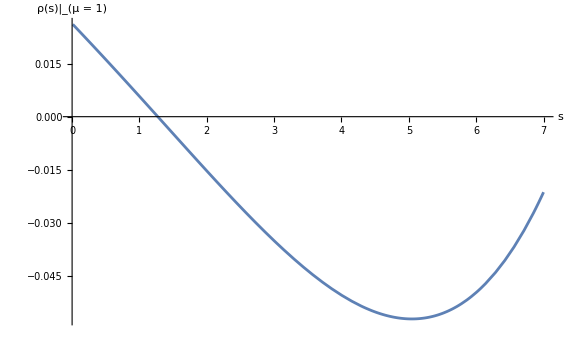
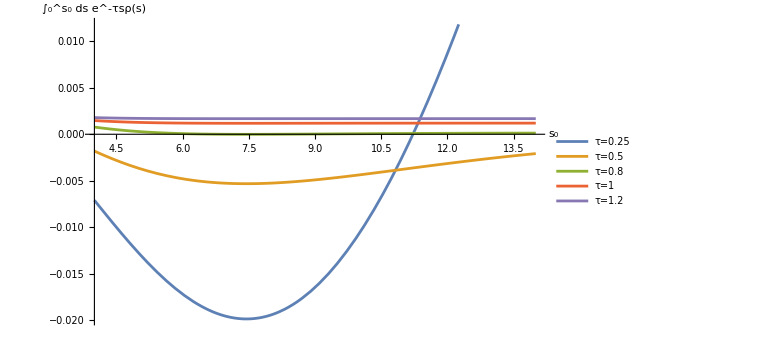

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

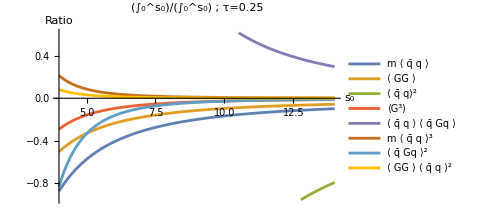
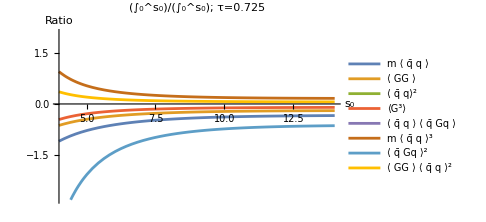
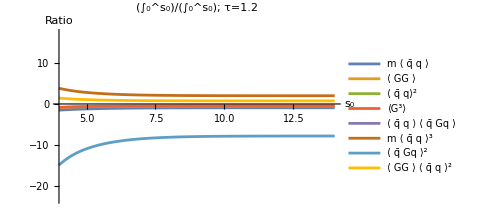

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

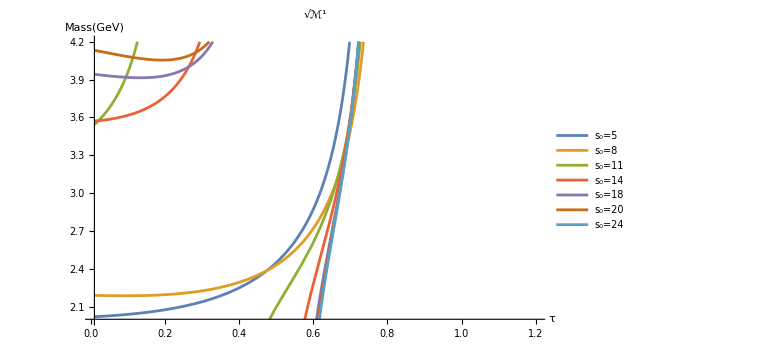
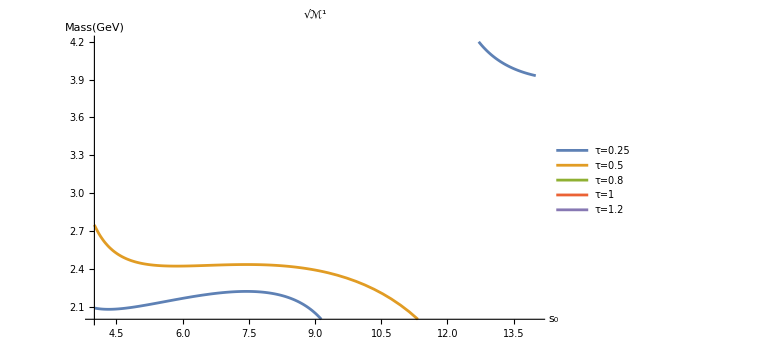

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5